# Curvature and Baryon Density

## Environment

```mathematica
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],CellContext->Notebook];
```

## Boxes

```mathematica
MakeBoxes[τ1, StandardForm] := SubscriptBox["τ", "1"]; 
MakeExpression[SubscriptBox["τ", "1"], StandardForm] := MakeExpression["τ1", StandardForm]; 
MakeBoxes[baryonDensity, StandardForm] := SubscriptBox["ρ", "b"]; 
MakeExpression[SubscriptBox["ρ", "b"], StandardForm] := MakeExpression["baryonDensity", StandardForm]; 
MakeBoxes[boltzmannConstant, StandardForm] := SubscriptBox["k", "b"]; 
MakeExpression[SubscriptBox["k", "B"], StandardForm] := MakeExpression["boltzmannConstant",StandardForm]; 
MakeBoxes[timeOfRecombination, StandardForm] := SubscriptBox["τ", "*"]; 
MakeExpression[SubscriptBox["τ", "*"], StandardForm] := MakeExpression["timeOfRecombination", StandardForm]; 
MakeBoxes[currentTemperature, StandardForm] := SubscriptBox["T", "0"]; 
MakeExpression[SubscriptBox["T", "0"], StandardForm] := MakeExpression["currentTemperature",StandardForm]; 
MakeBoxes[distanceComoving, StandardForm] := SubscriptBox["D", "C"]; 
MakeExpression[SubscriptBox["D", "C"], StandardForm] :=MakeExpression["distanceComoving", StandardForm]; 
MakeBoxes[electronDensity, StandardForm] := SubscriptBox["n", "e"]; 
MakeExpression[SubscriptBox["n", "e"], StandardForm] := MakeExpression["electronDensity",StandardForm]; 
MakeBoxes[freeElectronFraction, StandardForm] := SubscriptBox["X", "e"]; 
MakeExpression[SubscriptBox["X", "e"], StandardForm] := MakeExpression["freeElectronFraction",StandardForm]; 
MakeBoxes[hydrogenAbundance, StandardForm] := SubscriptBox["A", "H"]; 
MakeExpression[SubscriptBox["A", "H"], StandardForm] := MakeExpression["hydrogenAbundance",StandardForm]; 
MakeBoxes[hydrogenMass, StandardForm] := SubscriptBox["m", "H"]; 
MakeExpression[SubscriptBox["m", "H"], StandardForm] := MakeExpression["hydrogenMass", StandardForm]; 
MakeBoxes[heliumAbundance, StandardForm] := SubscriptBox["A", "He"]; 
MakeExpression[SubscriptBox["A", "He"], StandardForm] := MakeExpression["heliumAbundance",StandardForm]; 
MakeBoxes[heliumMass, StandardForm] := SubscriptBox["m", "He"]; 
MakeExpression[SubscriptBox["m", "He"], StandardForm] := MakeExpression["heliumMass", StandardForm]; 
MakeBoxes[hyperspherical, StandardForm] := SubscriptBox["S", "k"]; 
MakeExpression[SubscriptBox["S", "k"], StandardForm] := MakeExpression["hyperspherical", StandardForm]; 
MakeBoxes[hubbleConstant, StandardForm] := SubscriptBox["H", "0"]; 
MakeExpression[SubscriptBox["H", "0"], StandardForm] := MakeExpression["hubbleConstant", StandardForm]; 
MakeBoxes[flatCurvature, StandardForm] := SubscriptBox["k", "Z"]; 
MakeExpression[SubscriptBox["k", "Z"], StandardForm] := MakeExpression["flatCurvature", StandardForm]; 
MakeBoxes[negativeCurvature, StandardForm] := SubscriptBox["k", "N"]; 
MakeExpression[SubscriptBox["k", "N"], StandardForm] := MakeExpression["negativeCurvature", StandardForm]; 
MakeBoxes[photonDensity, StandardForm] := SubscriptBox["ρ", "γ"]; 
MakeExpression[SubscriptBox["ρ", "γ"], StandardForm] := MakeExpression["photonDensity",StandardForm]; 
MakeBoxes[positiveCurvature, StandardForm] := SubscriptBox["k", "P"]; 
MakeExpression[SubscriptBox["k", "P"], StandardForm] := MakeExpression["positiveCurvature", StandardForm]; 
MakeBoxes[randomConstant, StandardForm] := SubscriptBox["a", "B"]; 
MakeExpression[SubscriptBox["a", "B"], StandardForm] := MakeExpression["randomConstant", StandardForm]; 
MakeBoxes[redshiftFromTime, StandardForm] := SubscriptBox["z", "τ"]; 
MakeExpression[SubscriptBox["z", "τ"], StandardForm] := MakeExpression["redshiftFromTime",StandardForm]; 
MakeBoxes[redshiftOfRecombination, StandardForm] := SubscriptBox["z", "*"]; 
MakeExpression[SubscriptBox["z", "*"], StandardForm] := MakeExpression["redshiftOfRecombination", StandardForm];
MakeBoxes[scaleFactorFromTime, StandardForm] := SubscriptBox["a", "τ"]; 
MakeExpression[SubscriptBox["a", "τ"], StandardForm] := MakeExpression["scaleFactorFromTime",StandardForm]; 
MakeBoxes[soundHorizon, StandardForm] := SubscriptBox["s", "*"]; 
MakeExpression[SubscriptBox["s", "*"], StandardForm] := MakeExpression["soundHorizon", StandardForm]; 
MakeBoxes[v3, StandardForm] := SubscriptBox["v", "3"]; 
MakeExpression[SubscriptBox["v", "3"], StandardForm] := MakeExpression["v3", StandardForm]; 
MakeBoxes[thetaPrime, StandardForm] := SuperscriptBox["θ", "′"]; 
MakeExpression[Superscript["θ", "′"], StandardForm] := MakeExpression["thetaPrime", StandardForm]; 
MakeBoxes[thomsonScatteringCrossSection, StandardForm] := SubscriptBox["σ", "T"]; 
MakeExpression[SubscriptBox["σ", "T"], StandardForm] :=MakeExpression["thomsonScatteringCrossSection", StandardForm]; 
 MakeBoxes[timeFromRedshift, StandardForm] := SubscriptBox["τ", "z"]; 
MakeExpression[SubscriptBox["τ", "z"], StandardForm] := MakeExpression["timeFromRedshift",StandardForm]; 
MakeBoxes[timePrime, StandardForm] := SuperscriptBox["τ", "′"]; 
MakeExpression[SuperscriptBox["τ", "′"], StandardForm] := MakeExpression["timePrime", StandardForm]; 
MakeBoxes[a3, StandardForm] := SubscriptBox["a", "3"]; 
MakeExpression[SubscriptBox["a", "3"], StandardForm] := MakeExpression["a3",StandardForm]; 
MakeBoxes[kB, StandardForm] := SubscriptBox["k", "B"]; 
MakeExpression[SubscriptBox["k", "B"], StandardForm] := MakeExpression["kB",StandardForm];
```

## Units

```mathematica
s=1;
m=1;
cm=0.01 m;
kg=1;
g=0.001 kg;
J=(kg m^2)/s^2;
K=1;
km=1000 m;
yr=60 60 24 365.25 s;
kyr=1000 yr;
Myr=1000 kyr;
Gyr=1000 Myr;
pc=3.08567758 10^13 km;
kpc=1000 pc;
Mpc=1000 kpc;
Gpc=1000 Mpc;
```

## Constants

```mathematica
G=6.67408 10^-11 m^3/(kg s^2);
ℏ=6.62607004 10^-34 J s;
Subscript[k, B]=1.380649 10^-23 J/K;
Subscript[T, 0]=2.7255 K;
θ100=1.0411;
Subscript[A, He]=0.25;
Subscript[A, H]=0.75;
Subscript[m, He]=6.6464764 10^-27 kg;
Subscript[m, H]=1.6735575 10^-27 kg;
Subscript[σ, T]=6.6524 10^-29 m^2;
Subscript[ρ, b]=2.2937×10^-27 kg m^-3;
Subscript[ρ, γ]=7.775×10^-31 kg m^-3;
```

## Clear Variables

```mathematica
ClearAll[z,k,τ,Subscript[τ, 1],Subscript[a, 3],Subscript[v, 3]];
```

## Data

### Free Electron Fraction

This file is the output of the Recfast++ program .  It' s a collection of redshifts and the expected free election fraction at that time based on a cosmological model.

```mathematica
freeElectronFractionData=Import["C:\\Users\\DonaldAirey\\source\\repos\\recfast-cplusplus\\Recfast\\output\\Xe_Recfast.dat","Table"];
```

## Functions

```mathematica
x=Subscript[v, 3] τ-Subscript[a, 3]/2 τ^2;
Subscript[x, 0]=x/.{τ->Subscript[τ, 0]};
Subscript[x, 1]=x/.{τ->Subscript[τ, 1]};
```

### Time from Redshift

```mathematica
Subscript[τ, z][z_]=Subscript[τ, 0]/.Simplify[Solve[z==(Subscript[x, 1]-Subscript[x, 0])/Subscript[x, 0],Subscript[τ, 0]]][[1]]
```

(v_3+v_3 z-√((1+z) (v_3^2+v_3^2 z-2 a_3 v_3 τ_1+a_3^2 τ_1^2)))/(a_3+a_3 z)

### Redshift from Time

```mathematica
Subscript[z, τ][τ_]=z/.Simplify[Solve[z==(Subscript[x, 1]-Subscript[x, 0])/Subscript[x, 0],z]/.{Subscript[τ, 0]->τ}][[1]]
```

-((τ-τ_1) (-2 v_3+a_3 (τ+τ_1)))/(τ (-2 v_3+a_3 τ))

### Scale Factor

```mathematica
a[τ_]=Simplify[1/(1+Subscript[z, τ][τ])]
```

(τ (-2 v_3+a_3 τ))/(τ_1 (-2 v_3+a_3 τ_1))

### Comoving Distance from Redshift

```mathematica
Subscript[D, C][z_]=(z Subscript[τ, 1] (2 Subscript[v, 3]-Subscript[a, 3] Subscript[τ, 1]))/(2+z);
```

### Electron Number Density

```mathematica
Subscript[X, e]=Interpolation[freeElectronFractionData⟦All,{1,2}⟧];
```

```mathematica
Subscript[n, e][τ_]=Subscript[X, e][Subscript[z, τ][τ]] Subscript[ρ, b]/(Subscript[A, H] Subscript[m, H]+Subscript[A, He] Subscript[m, He])(1+Subscript[z, τ][τ])^3;
```

### Scale Factor from Time

### Scattering Rate

Note that the electron number density, n_e is in units of cm^-3. Thompson cross section, σ_T, is in units of cm^2. The scale factor, a, is unit-less.  Note that we convert the value to units of s^-1 by multiplying by the speed of light.  This is because the Optical Depth integrates over (conformal) time.  When we multiply inverse time by time,  ⅆ η', we get a unit-less value which are the units of Optical Depth.  All of the textbooks seem to leave this important step out.  It’s critical that the units give us the right answer.

```mathematica
ScatteringRate[τ_]:=Subscript[n, e][τ] Subscript[σ, T] a[τ](Subscript[v, 3]-Subscript[a, 3] τ)
```

### Optical Depth

```mathematica
OpticalDepth[τ_]:=NIntegrate[ScatteringRate[τ'],{τ',τ,Subscript[τ, 1]}]
```

### Time of Recombination

```mathematica
SubStar[τ]:=τ/.Quiet[FindRoot[OpticalDepth[τ]==1,{τ,Subscript[τ, z][1000]}]];
```

### Baryon-Photon Momentum Density Ratio

```mathematica
R[τ_]=3/4(Subscript[ρ, b](1+Subscript[z, τ][τ])^3)/(Subscript[ρ, γ](1+Subscript[z, τ][τ])^4);
```

### Sound Horizon

```mathematica
SubStar[s][τ_?NumericQ]:=NIntegrate[(Subscript[v, 3]-Subscript[a, 3] τ')/(√(3×(1+R[τ']))),{τ',0,τ}];
```

### Angular Scale

ThemetricforQESis
ConditionalExpression[ds^2==-(v_3+a_3 t)^2 dt^2+(t/t_1^2)^2(dr^2+Sin[r√k]/(√k))^2(ⅆ θ^2+sin^2 θ dϕ^2)),k>0]
ConditionalExpression[ds^2==-(v_3+a_3 t)^2 dt^2+(t/t_1^2)^2(dr^2+(Sinh[r√Abs[k]]/(√Abs[k]))^2(ⅆ θ^2+sin^2 θ dϕ^2)),k<0]
We want to solve the metric for θ,a measured angle in the sky having a physical length of s_*at a fixed distance of r,the distance to the last scattering.

```mathematica
Subscript[k, P][k_,r_,SubStar[s]:_]:=θ/.Solve[SubStar[s]==∫_0^θ Sin[r √k]/(√k)ⅆ θ',θ]⟦1⟧
Subscript[k, Z][k_,r_,SubStar[s]:_]:=θ/.Solve[SubStar[s]==r θ,θ][[1]]
Subscript[k, N][k_,r_,SubStar[s]:_]:=θ/.Solve[SubStar[s]==∫_0^θ Sinh[r √Abs[k]]/(√Abs[k])ⅆ θ',θ]⟦1⟧
Subscript[S, k][k_,r_,SubStar[s]:_]:=If[k>0,Subscript[k, P][k,r,SubStar[s]],If[k==0,Subscript[k, Z][k,r,SubStar[s]],Subscript[k, N][k,r,SubStar[s]]]]
```

```mathematica
AngularScale[k_?NumericQ]:=Block[{z=Subscript[z, τ][SubStar[τ]]},Subscript[S, k][k,Subscript[D, C][z],SubStar[s][Subscript[τ, z][z]]]]
```

## QES Constants

```mathematica
Subscript[v, 3]=3.17840613545762×10^8;
Subscript[a, 3]=3.64661613355436×10^-11;
Subscript[τ, 1]=4.94928856911811×10^17;
```

```mathematica
Subscript[ρ, b](1+1300)^3
```

5.0509×10^-18

## Optical Depth

$Aborted

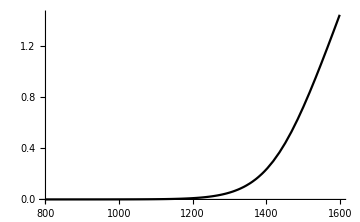

```mathematica
opticalDepthPlot = Plot[OpticalDepth[Subscript[τ, z][z]],{z,2000,1000},PlotStyle->{Black},PlotRange->{{2000,1000},{0,4}}];
Show[{opticalDepthPlot},ImageSize->Medium]
```

## Critical Density

The optimization above is inconclusive because, as we approach a perfect flatness, there isn’t enough information in the signal. So we skip ahead and calculate the angular scale for a flat topology.

```mathematica
SubStar[τ]
Subscript[z, τ][SubStar[τ]]
SubStar[s][3.69*^14]
```

4.8041×10^14

1000.

5.12486×10^22

```mathematica
CopyToClipboard@ExportString[{Subscript[z, τ][SubStar[τ]],Subscript[ρ, b][Subscript[τ, 1],0],SubStar[s][SubStar[τ]]},"TSV"];
```

```mathematica
AngularScale[-4.212245600469784*^-53]100
```

0.0115385